## R0 Bound subfigure

```mathematica
fixLegend[size_][legend_]:=ReplaceAll[legend,{g_Graphics:>Show[g,ImageSize->Automatic->{Automatic,size},BaselinePosition->Axis],Pane->Function@#}]
MakeBoxes[stripGridAlignemnt[expr_],form_]^:=ReplaceAll[MakeBoxes[expr,form],Rule[GridBoxAlignment,_]->Sequence[]]
```

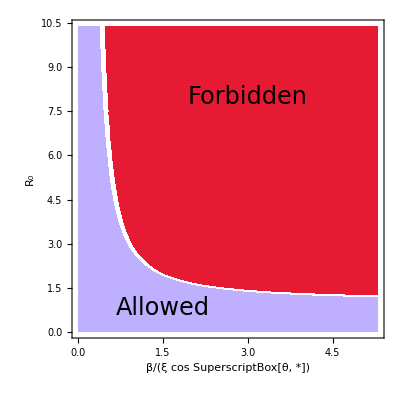
-Graphics-(A)

```mathematica
r0boundplot=Plot[{E^(1/x), 1},{x,0,10}, PlotRange->{0, 10}, PlotStyle->{Line, Dashed}, PlotLegends->{"max R_0", "R_0=1"},AxesLabel->{"β/ξ","R_0"},AxesStyle->Black];
r0bounddensityplot = 
DensityPlot[UnitStep[E^(1/x)-R0],{x,0,5.3},{R0,0,10.4},
PlotPoints->10, 
AxesStyle->Black,
BaselinePosition->Axis,AxesOrigin->{0,5.175},
FrameLabel->{{Style[HoldForm["R_0"],24,Black],None},{Style[HoldForm["β/(ξ cos SuperscriptBox[θ, *])"],24,Black],Style["sometext",24,White]}},
ColorFunction->Function[y,ColorData["BrightBands"][0.3*(y)]],
FrameTicksStyle->Directive[FontSize->24,Black],
ImageSize->Automatic->300 ];

r0boundfiga = Show[r0bounddensityplot, Graphics[Text[Style["Allowed",24],{1.5,0.8}]],Graphics[Text[Style["Forbidden",24],{3,8}]]];
r0boundfig = stripGridAlignemnt@Labeled[r0boundfiga,{Style["(A)",24,Black]},{{Top, Left}}]
```

## Dynamical Bounds figure

```mathematica
NN=10^9;
```

```mathematica
fixLegend[size_][legend_]:=ReplaceAll[legend,{g_Graphics:>Show[g,ImageSize->Automatic->{Automatic,size},BaselinePosition->Axis],Pane->Function@#}]
MakeBoxes[stripGridAlignemnt[expr_],form_]^:=ReplaceAll[MakeBoxes[expr,form],Rule[GridBoxAlignment,_]->Sequence[]]
```

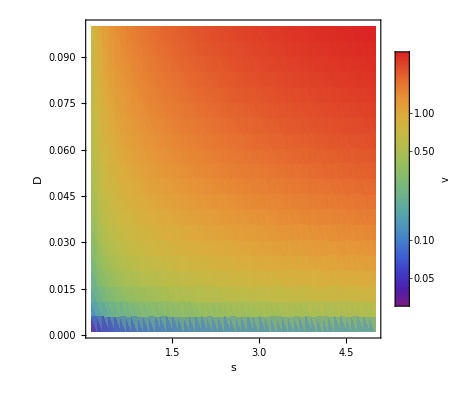

```mathematica
velExpr[s_,DD_]:=DD^(2/3)s^(1/3)(24*Log[v*NN*s*DD^(1/3)*s^(2/3)])^(1/3)-v
(*
(*** Uncomment to plot velocity as a function of s ***)
velTab = Flatten[Evaluate@Table[{s, DD, v/.NSolve[velExpr[s,DD]==0, v,Reals][[2]]},{s,.1,5,.1},{DD,10^-3,10^-1,(10^-1-10^-3)/20}],1];
velTab;
velplot=ListDensityPlot[velTab,FrameLabel->{{HoldForm[D],None},{HoldForm[s],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->BarLegend[Automatic, LegendLabel->"v"],ScalingFunctions->"Log" , ColorFunction->"Rainbow"];
velplot
*)
```

```mathematica
maxVelExpr[β_,DD_]:=velExpr[1/β,DD]
maxVelTab = Flatten[Evaluate@Table[{β, DD, v/.NSolve[maxVelExpr[β,DD]==0, v,Reals][[2]]},{β,.1,5.3,.4},{DD,10^-3,10^-1,(10^-1-10^-3)/20.}],1];
```

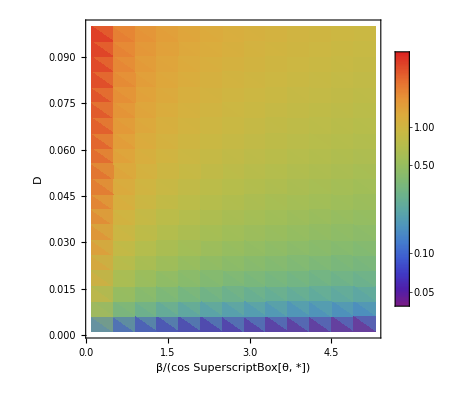
-Graphics-(B)

```mathematica
maxvelplot=ListDensityPlot[maxVelTab,
FrameLabel->{{Style[HoldForm[D],24,Black],None},{Style[HoldForm["β/(cos SuperscriptBox[θ, *])"],24,Black],Style["max v",24,Black]}},
BaselinePosition->Axis,AxesOrigin->{0,0.05},
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize-> 24,Black},LegendFunction->fixLegend[310]],After],
ScalingFunctions->"Log" , ColorFunction->"Rainbow",
FrameTicksStyle->Directive[FontSize->24,Black],
ImageSize->Automatic->300];
maxvelfig=stripGridAlignemnt@Labeled[maxvelplot,{Style["(B)",24,Black]},{{Top, Left}}]
```

```mathematica
stdExpr[s_,DD_]:= Sqrt[Abs[v/s]/.NSolve[velExpr[s,DD]==0,v,Reals][[2]]]
```

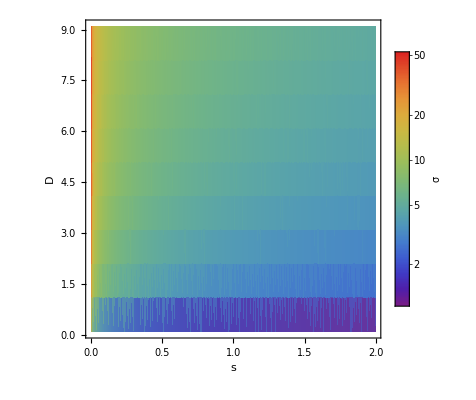

```mathematica
(*
(*** Uncomment to plot standard deviation as a function of s ***)
stdTab = Flatten[Evaluate@Table[{s, DD, stdExpr[s,DD]},{s,.001,2,0.005},{DD,.1,10,1}],1];
stdplot=ListDensityPlot[stdTab,FrameLabel->{{HoldForm[D],None},{HoldForm[s],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->BarLegend[Automatic, LegendLabel->"σ"],ScalingFunctions->"Log" , ColorFunction->"Rainbow"]
*)
```

```mathematica
minStdExpr[β_, DD_]:=stdExpr[1/β, DD]
minStdTab = Flatten[Evaluate@Table[{β, DD, minStdExpr[β,DD]},{β,.1,5.3,.4},{DD,10^-3,10^-1,(10^-1-10^-3)/20.}],1];
```

```mathematica
minStdplot=ListDensityPlot[minStdTab,
BaselinePosition->Axis,AxesOrigin->{0,0.05},
FrameLabel->{{Style[HoldForm[D],24,Black],None},{Style[HoldForm["β/(cos SuperscriptBox[θ, *])"],24,Black],Style["min σ",24,Black]}},
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize-> 24,Black},LegendFunction->fixLegend[310]],After], 
ScalingFunctions->"Log" , ColorFunction->"Rainbow", 
FrameTicksStyle->Directive[FontSize->24,Black],
ImageSize->Automatic->300];
```

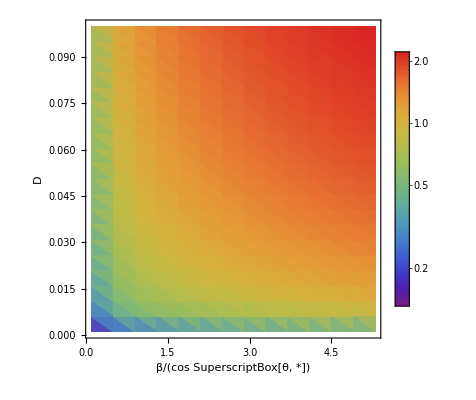
-Graphics-(C)

```mathematica
minStdfig=stripGridAlignemnt@Labeled[minStdplot,{Style["(C)",24,Black]},{{Top, Left}}]
```

```mathematica
α=1.66;
```

```mathematica
minMrcaTimeVal[β_,DD_]:=α*minVarExpr[β,DD]/(2*DD)
minMrcaTimeTab = Flatten[Table[{β,DD, minMrcaTimeVal[β,DD]}, {β,.1,5.3,.4},{DD,10^-3,10^-1,(10^-1-10^-3)/20.}],1];
```

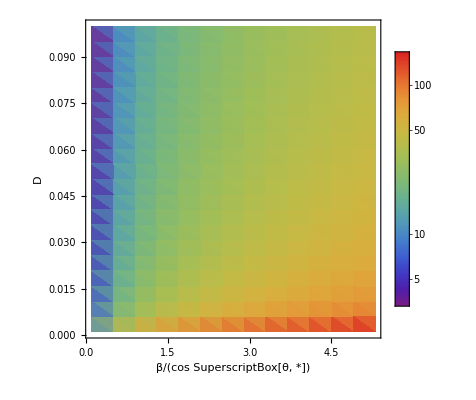
-Graphics-(D)

```mathematica
minMrcaTimeplot=ListDensityPlot[minMrcaTimeTab,
BaselinePosition->Axis,AxesOrigin->{0,0.05},
FrameLabel->{{Style[HoldForm[D],24, White],None},{Style[HoldForm["β/(cos SuperscriptBox[θ, *])"],24, Black],Style["min t_MRCA",24,Black]}},
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize-> 24,Black},LegendFunction->fixLegend[310]],After],
ScalingFunctions->"Log" , ColorFunction->"Rainbow",
FrameTicksStyle->Directive[FontSize->24, Black],
ImageSize->Automatic->300 ];
minMrcaTimefig = stripGridAlignemnt@Labeled[minMrcaTimeplot,{Style["(D)",24,Black]},{{Top, Left}}]
```

```mathematica
dataplots=GraphicsGrid[{{r0boundfig,maxvelfig},{minStdfig,minMrcaTimefig}}, ImageSize->1000]
```

-Graphics-